### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/RandomLotka-Volterra

### Keywords

Details

# Random Lotka-Volterra

Here we consider a Lotka-Volterra competition model with random competition coefficients, following Kessler & Shnerb (2015).  Here n_i is population size, ι is the immigration rate, 𝒦 is the carrying capacity, c_(i,j) are competition coefficients (i≠j), and 𝒞 sets the overall strength of interspecific competition.

-Graphics-

```mathematica
Needs["EcoEvo`"];
```

Set up model:

```mathematica
SetModel[{
Guild[n]->{
Equation:>ι+(1-(Subscript[n, i]+Sum[If[i≠j,Subscript[c, i,j] Subscript[n, j],0],{j,Subscript[𝒩, n]}]𝒞)/𝒦)Subscript[n, i]
},
Interaction[c]->{Guilds->{n,n},Range->Interval[{-∞,∞}]},
Parameters->{ι≥0,𝒞>0,𝒦>0,σr>0}
}];
```

Simulate two species competing:

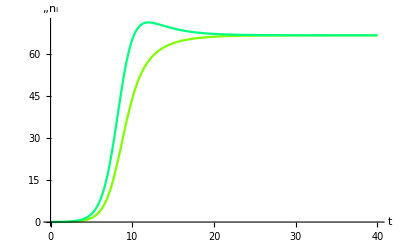

```mathematica
ι=0;𝒦=100;𝒞=1;
sol=EcoSim[{Subscript[c, 1,2]->0.5,Subscript[c, 2,1]->0.5},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.02},40];
PlotDynamics[sol]
```

Plot the phase plane:

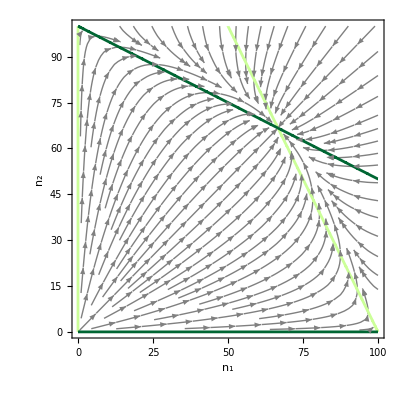

```mathematica
PlotEcoPhasePlane[{Subscript[c, 1,2]->0.5,Subscript[c, 2,1]->0.5},{Subscript[n, 1],0,𝒦},{Subscript[n, 2],0,𝒦}]
```

Now make a random competition matrix cmat:

```mathematica
σr=0.5;
𝒞=0.85;
𝒦=100;
nsp=5;
```

```mathematica
SeedRandom[1];
cmat=Table[If[i==j,0,RandomVariate[GammaDistribution[1/σr^2,σr^2]]],{i,nsp},{j,nsp}];
cmat//MatrixForm
```

(0 | 0.351092 | 0.648432 | 1.59724 | 0.603855
1.36063 | 0 | 1.03074 | 0.483342 | 0.597855
2.09053 | 1.17383 | 0 | 0.595708 | 2.09886
0.832671 | 1.60409 | 0.764326 | 0 | 0.506859
1.0325 | 0.883507 | 0.503994 | 0.877812 | 0)

Simulate dynamics.  Note that ArrayToRuleList is applied automatically when interactions are given without a subscript:

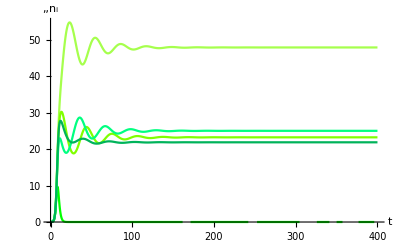

{n_1→47.8851,n_2→23.2311,n_3→-3.81312×10^-63,n_4→25.013,n_5→21.8655}

```mathematica
sol=EcoSim[{c->cmat},Table[Subscript[n, i]->0.01,{i,nsp}],400];
PlotDynamics[sol]
FinalSlice[sol]
```

Find the attractor and verify its stability:

```mathematica
eq=FindEcoAttractor[{c->cmat}]
EcoEigenvalues[{c->cmat},eq]
```

{n_1→47.8851,n_2→23.2311,n_3→0,n_4→25.013,n_5→21.8655}

{-1.,-0.599425,-0.0333591+0.201328 ⅈ,-0.0333591-0.201328 ⅈ,-0.113229}

Check its invasibility:

```mathematica
Table[Inv[{c->cmat},eq,Subscript[n, i]],{i,nsp}]
```

InvSPS::nonzero: Warning: invasion rate only defined for rare invaders.

General::stop: Further output of InvSPS :: nonzero will be suppressed during this calculation.

{0.,-2.22045×10^-16,-0.599425,1.11022×10^-16,0.}

A different random number seed leads to a different outcome:

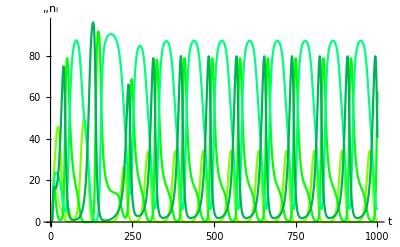

```mathematica
SeedRandom[2];
cmat=Table[If[i==j,0,RandomVariate[GammaDistribution[1/σr^2,σr^2]]],{i,nsp},{j,nsp}];
sol=EcoSim[{c->cmat},Table[Subscript[n, i]->0.01,{i,nsp}],1000];
PlotDynamics[sol]
```

Now all of the valid equilibria have eigenvalues with positive real parts:

```mathematica
eq=SelectValid[NSolveEcoEq[{c->cmat}]]
SelectEcoStable[{c->cmat},eq]
```

{{n_1→0,n_2→0,n_3→0,n_4→0,n_5→0},{n_1→100.,n_2→0,n_3→0,n_4→0,n_5→0},{n_1→0,n_2→100.,n_3→0,n_4→0,n_5→0},{n_1→0,n_2→0,n_3→100.,n_4→0,n_5→0},{n_1→0,n_2→0,n_3→0,n_4→100.,n_5→0},{n_1→0,n_2→0,n_3→0,n_4→0,n_5→100.},{n_1→23.4975,n_2→91.4349,n_3→0,n_4→0,n_5→0},{n_1→67.3824,n_2→0,n_3→53.8692,n_4→0,n_5→0},{n_1→0,n_2→2.68902,n_3→95.2246,n_4→0,n_5→0},{n_1→52.4989,n_2→0,n_3→0,n_4→36.4696,n_5→0},{n_1→0,n_2→68.9835,n_3→0,n_4→44.7893,n_5→0},{n_1→0,n_2→0,n_3→11.1471,n_4→94.1452,n_5→0},{n_1→27.4122,n_2→0,n_3→0,n_4→0,n_5→61.5496},{n_1→20.2019,n_2→90.4426,n_3→0,n_4→3.16766,n_5→0},{n_1→45.3629,n_2→0,n_3→52.3002,n_4→17.6351,n_5→0},{n_1→27.146,n_2→13.602,n_3→0,n_4→0,n_5→52.1253},{n_1→0,n_2→17.4468,n_3→63.8943,n_4→0,n_5→11.7594},{n_1→43.3703,n_2→0,n_3→0,n_4→32.7498,n_5→11.8487},{n_1→0,n_2→0,n_3→22.6443,n_4→78.35,n_5→7.82851},{n_1→26.1719,n_2→37.1438,n_3→0.424466,n_4→0,n_5→36.0315},{n_1→0,n_2→8.67169,n_3→22.6651,n_4→56.4894,n_5→19.7917},{n_1→17.5733,n_2→28.8063,n_3→12.509,n_4→12.0135,n_5→29.7652}}

{}

Increasing the number of species:

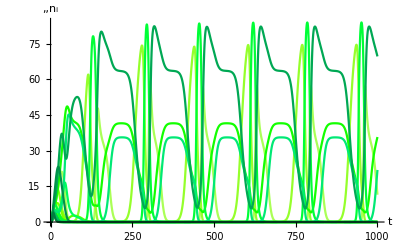

```mathematica
nsp=20;
tmax=1000;
SeedRandom[3];
cmat=Table[If[i==j,0,RandomVariate[GammaDistribution[1/σr^2,σr^2]]],{i,nsp},{j,nsp}];
sol=EcoSim[{c->cmat},Table[Subscript[n, i]->0.01,{i,nsp}],tmax];
PlotDynamics[sol]
```

Another way to see the dynamics:

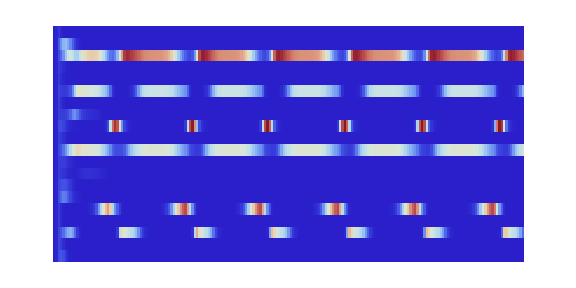

```mathematica
PlotGuild[sol]
```

### References

Kessler DA, Shnerb NM. 2015. Generalized model of island biodiversity. Physical Review E 91: 042705.

More About

Related Tutorials

Related Wolfram Education Group Courses